ω at surface: 0.5

ω at infinity: 0.404816

Mean modification factor: 0.466212

Time elapsed: 2.367612

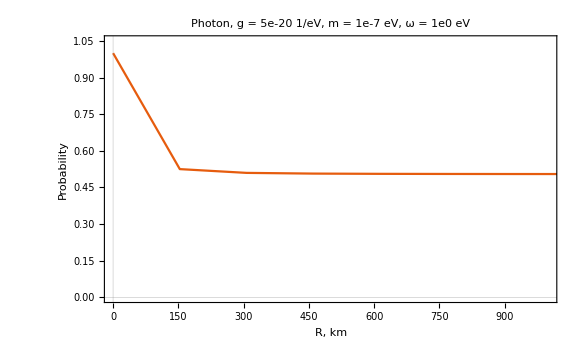

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

(*С каких углов считаем излучение*)
lowerAngle=0.1;
upperAngle=Pi/2.01;
nSteps=6;

(*Параметры АЛП*)
ω0=0.5;
g=6*10^(-20);
m=10^(-8);

(*Конфигурация поля*)
angleObserver = Pi/6;
BSurf = 15*10^12;
R0 = 12;
period =7;

(*Конфигурация точки излучения*)
(*По x мы итерируемся, r - расстояние от поверхности звезды*)
r:=Sqrt[(R0 Sin[angleEmission]+x)^2 + (R0 Cos[angleEmission]+x(Rlc/Tan[angleObserver]-R0 Cos[angleEmission])/(Rlc-R0 Sin[angleEmission]))^2];

angleIteration:=ArcTan[(R0 Sin[angleEmission]+x)/(R0 Cos[angleEmission]+(x(Rlc/Tan[angleObserver]-R0 Cos[angleEmission])/(Rlc - R0 Sin[angleEmission])))];

(*Размер области, должен быть равен радиусу*)
startingPoint = R0;

(*Радиус светового цилиндра*)
Rlc=47713*period;
upperLimit:=500000;

(*Значения поля (диполь)*)
bRep:={bRad->BSurf*Cos[angleIteration]*(R0/r)^3,
	bTheta->0.5*BSurf*Sin[angleIteration]*(R0/r)^3,
	bPhi->0};

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/R0))/(1-(4.134/r))];

(*Без красного смещения*)
(*ω:=ω0;*)

(*Элементы матрицы М*)
deltaMTheta:=5.0*10^7*bTheta*g;
deltaMPhi:=5.0*10^7*bPhi*g;

deltaMass:=2.5*10^9*m^2*(1/ω);

deltaPlasma:=0*3.1*10^(-12)*(bRad*Cos[angleIteration]-bTheta*Sin[angleIteration])*(1/period)*(1/ω);

deltaCEDTheta:=-4.5*10^(-22)*ω*bTheta^2;
deltaCEDPhi:=-4.5*10^(-22)*ω*bPhi^2;

(*Матрица М*)
mat:={{deltaPlasma+deltaCEDTheta,0,-ⅈ deltaMTheta},
	{0,deltaPlasma+deltaCEDPhi,-ⅈ deltaMPhi},
	{ⅈ deltaMTheta,ⅈ deltaMPhi,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
rmat[x_]:={{r11[x],r12[x],r13[x]},{r21[x],r22[x],r23[x]},{r31[x],r32[x],r33[x]}};

(*Список начальных условий*)rmat0={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};

t = Table[
(*Угол от 0 до 2.01*)
angleEmission=k;

(*Решаем систему*)
eqs=NDSolve[Join[{ⅈ rmat'[x]==rmat[x].mat-mat.rmat[x]},rmat0],{r11[x],r22[x],r33[x]},{x,0,upperLimit}, MaxSteps->10^8, AccuracyGoal->5];
Re[r11[x]+r22[x]/.First[eqs]/.x->(upperLimit-1)]
,{k,lowerAngle,upperAngle,upperAngle/nSteps}];

result=Mean[t];
Print["ω at surface: ",ω0];
Print["ω at infinity: ",ω/.x->(upperLimit-1)];
Print["Mean modification factor: ",result];
Print["Time elapsed: ",AbsoluteTime[]-time];

p1=Plot[Re[Evaluate[{r11[x]+r22[x]}/.eqs]],{x,0,upperLimit},PlotRange->{{0,1000},{0.0,1.05}},PlotTheme->"Scientific",PlotLabel->"Photon, g = 5e-20 1/eV, m = 1e-7 eV, ω = 1e0 eV", FrameLabel->{"R, km","Probability"}]

(*bb=6;
StringForm["The value of x is ``.",bb]
Export[ToString[m]<>".csv",m];*)
```

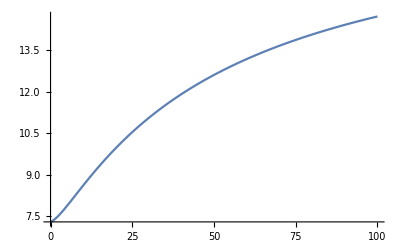

```mathematica
ω0=1;
Plot[{Abs[deltaMTheta]/Abs[deltaPlasma]}/.bRep,{x,0,100}]
```